```mathematica
aco = ActiveClassification[# > 50 &, {2, 5, 58, 74, 17, 29, 66, 12, 90, 77}]
```

ActiveClassificationObject[…]

```mathematica
c = aco["ClassifierFunction"]
```

ClassifierFunction[…]

```mathematica
c[{35, 57, 18, 100, 173, 9}]
```

{False,True,False,True,True,False}

```mathematica
aco=ActiveClassification[#>5&,Interval[{0,10}]]
```

ActiveClassificationObject[…]

```mathematica
aco = ActiveClassification[PositiveSemidefiniteMatrixQ, RandomReal[1, {2, 2}] &]
```

ActiveClassificationObject[…]

```mathematica
c = aco["ClassifierFunction"]
```

ClassifierFunction[…]

```mathematica
aco["Properties"]
```

{OracleFunction,EvaluationHistory,Method,Properties,LearningCurve,TrainingHistory,ClassifierFunction,ClassifierMeasurementsObject}

```mathematica
aco["TrainingHistory"]
```

Dataset[<>]

```mathematica
f[point_] := RegionMember[Disk[], point];
```

```mathematica
nsampler[point_] := point + RandomReal[{-.1, .1}, 2]
```

```mathematica
aco = ActiveClassification[f, {{1.0, 0.4}, {0.3, 1}}-> nsampler]
```

ActiveClassificationObject[…]

```mathematica
r1 = Rectangle[{40, 70}, {60, 90}];
r2 = RegionUnion[Rectangle[{40, 90}, {60, 120}], Rectangle[{60, 70}, {80, 120}]];
```

```mathematica
r3 = RegionUnion[Rectangle[{40, 120}, {80, 190}], Rectangle[{80, 70}, {100, 190}]];
```

```mathematica
reg = RegionUnion[r1, r2, r3];
```

```mathematica
f[{x_, y_}] := Which[
RegionMember[r1, {x, y}], "Low",
RegionMember[r2, {x, y}], "Ideal",
RegionMember[r3, {x, y}], "High",
True, "Wrong Input"];
aco = ActiveClassification[f, reg, Method -> "Randomized"]
```

ActiveClassificationObject[…]

```mathematica
apo = ActivePrediction[#+2 &, {2.0, 4.3, 9.1, 13.4, 20.5}]
```

ActivePredictionObject[…]

```mathematica
p = apo["PredictorFunction"]
```

PredictorFunction[…]

```mathematica
p[{1.2, 2.3, 7.8}]
```

{4.10333,5.02,9.60333}

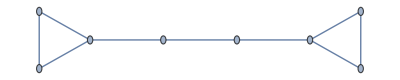

```mathematica
g = Graph[{1 <-> 2, 2<-> 3, 1 <-> 3, 3 <-> 4, 4 <-> 5, 7 <-> 6, 8<->6, 5 <->7, 7<-> 8}]
```

```mathematica
FindGraphCommunities[g]
```

{{1,2,3},{7,6,8},{4,5}}

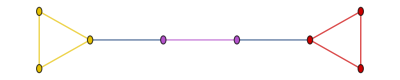

```mathematica
HighlightGraph[g, Map[Subgraph[g, #] &, %]]
```

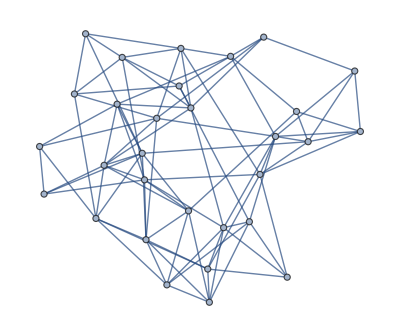

```mathematica
RandomGraph[WattsStrogatzGraphDistribution[30, 0.3, 3]]
```

```mathematica
CommunityGraphPlot[%, FindGraphCommunities[%]]
```

-Graphics-

```mathematica
FindGraphCommunities[-Graphics-]
```

{{1,2},{3,4},{5,6}}

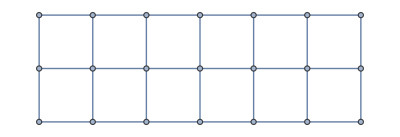

```mathematica
g = GridGraph[{3, 7}]
```

```mathematica
N[GraphAssortativity[g, FindGraphCommunities[g]]]
```

0.665422

```mathematica
N[GraphAssortativity[g, FindGraphCommunities[g, Method-> "VertexMoving"]]]
```

0.713219

```mathematica
g = ExampleData[{"NetworkGraph", "ZacharyKarateClub"}];
h = FindGraphCommunities[g, Method-> "Hierarchical"]
```

{{9,10,26,24,25,28,29,30,27,31,32,33,15,16,19,21,23,34},{2,1,3,4,5,6,7,8,11,12,13,14,17,18,20,22}}

```mathematica
CommunityGraphPlot[g, h]
```

-Graphics-

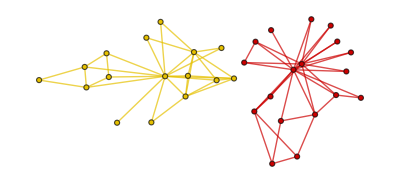

```mathematica
HighlightGraph[g, Subgraph[g, #] & /@ h, GraphHighlightStyle-> "DehighlightHide"]
```

```mathematica
data = RandomVariate[NormalDistribution[], 10^3];
d = SmoothKernelDistribution[data];
```

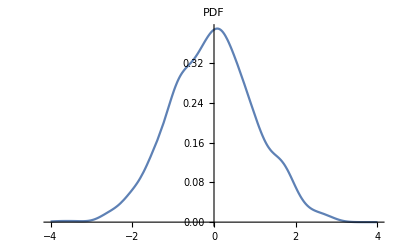
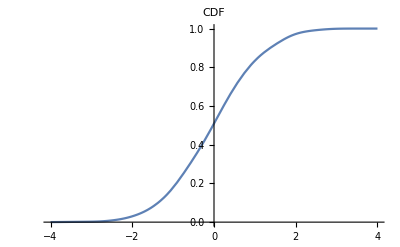

```mathematica
Table[Plot[f[d, x], {x, -4, 4}, PlotLabel-> f], {f, {PDF, CDF}}]
```

```mathematica
Moment[d, 2]
```

1.12129

```mathematica
Quantile[d, 0.95]
```

1.76028

```mathematica
data = RandomVariate[BinormalDistribution[0.75], 10];
d = SmoothKernelDistribution[data];
```

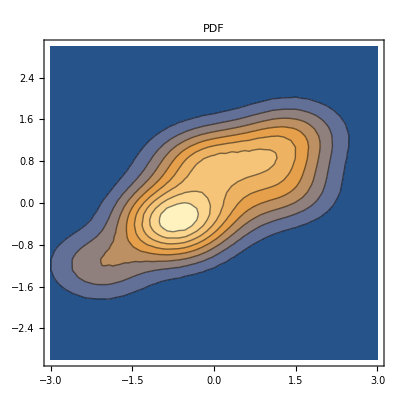
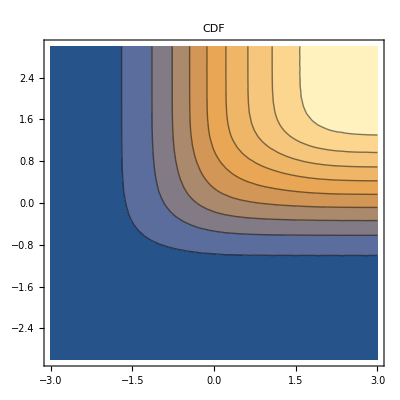

```mathematica
Table[ContourPlot[f[d, {x, y}], {x, -3, 3}, {y, -3, 3}, PlotLabel-> f, PlotRange-> All], {f, {PDF, CDF}}]
```

```mathematica
Covariance[d] // MatrixForm
```

(1.54271 | 0.650557
0.650557 | 0.766485)

```mathematica
Moment[d, {1, 2}]
```

-0.01381

```mathematica
data = RandomVariate[NormalDistribution[], 10^4];
```

```mathematica
d = SmoothKernelDistribution[data];
```

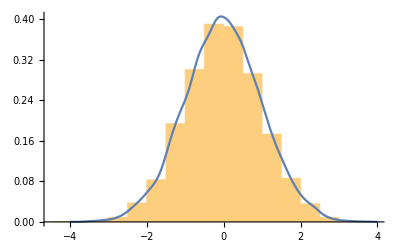

```mathematica
Show[Histogram[data, Automatic, "PDF"], Plot[PDF[d, x], {x, -4, 4}]]
```

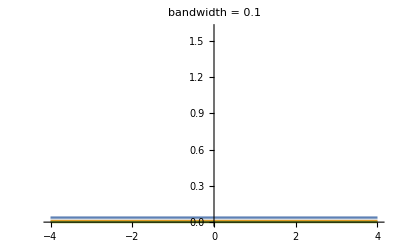
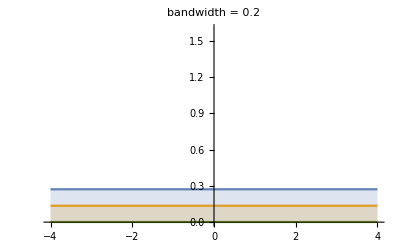
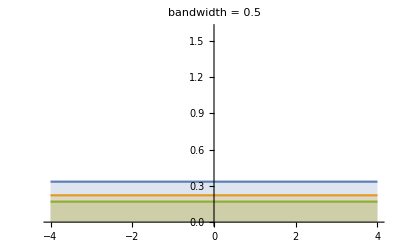
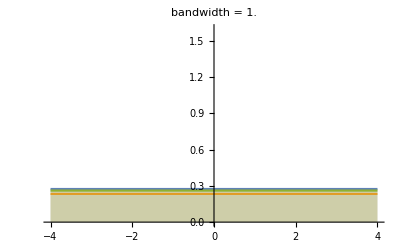

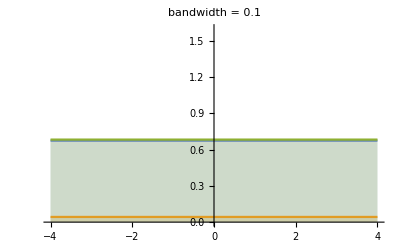
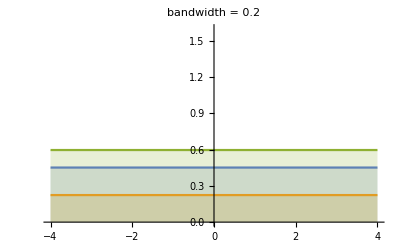
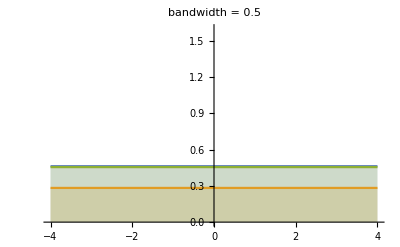
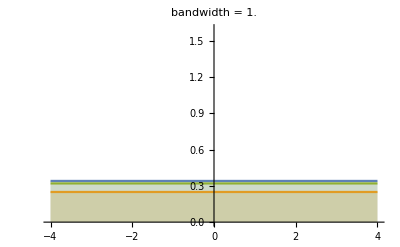

```mathematica
data=RandomVariate[NormalDistribution[],5];
bw={.1,.2,.5,1.0};
Table[Plot[PDF[SmoothKernelDistribution[data,i],x]// Evaluate,{x,-4,4},PlotLabel->Row[{"bandwidth = ",i}],PlotRange->{0,1.6},Filling->Axis],{i,bw}]
```

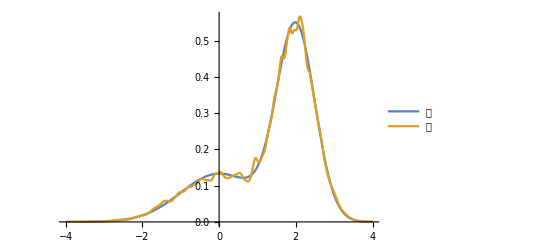

```mathematica
data=RandomVariate[𝒹=MixtureDistribution[{1,2},{NormalDistribution[],NormalDistribution[2,1/2]}],10^4];
𝒟=SmoothKernelDistribution[data,{"Adaptive",Automatic,.5}];
Plot[{PDF[𝒹,x],PDF[𝒟,x]},{x,-4,4},PlotLegends->{"𝒹","𝒟"}]
```

```mathematica
data = RandomVariate[NormalDistribution[], {10, 3}];
```